```mathematica
Series[BesselJ[0,x],{x,0,50}]
```

1-x^2/4+x^4/64-x^6/2304+x^8/147456-x^10/14745600+x^12/2123366400-x^14/416179814400+x^16/106542032486400-x^18/34519618525593600+x^20/13807847410237440000-x^22/6682998146554920960000+x^24/3849406932415634472960000-x^26/2602199086312968903720960000+x^28/2040124083669367620517232640000-x^30/1836111675302430858465509376000000+x^32/1880178355509689199068681601024000000-x^34/2173486178969200714123395930783744000000+x^36/2816838087944084125503921126295732224000000-x^38/4067514198991257477227662106371037331456000000+x^40/6508022718386011963564259370193659730329600000000-x^42/11480152075232925103727353529021615764301414400000000+x^44/22225574417650943000816156432185848119687538278400000000-x^46/47029315467749395389726987010505254621258830997094400000000+x^48/108355542837694606977930978072204106647380346617305497600000000-x^50/270888857094236517444827445180510266618450866543263744000000000000+O[x]^51

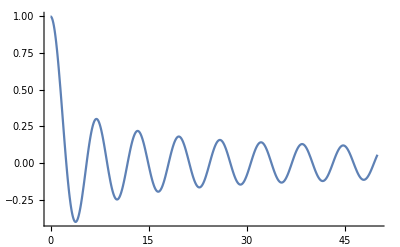

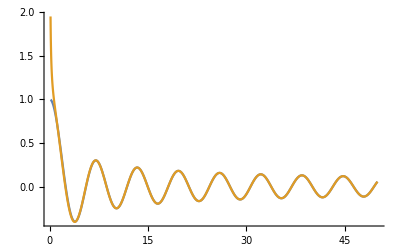

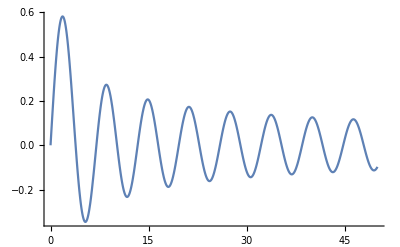

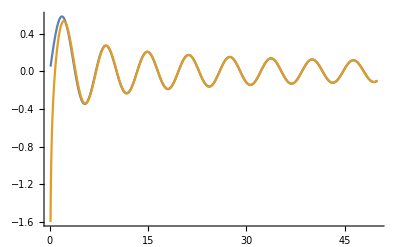

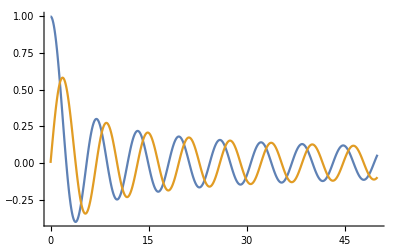

```mathematica
Plot[BesselJ[0,x],{x,0,50},PlotRange->All]

Plot[{BesselJ[0,x],√(2/(π x))Cos[x-π/4]},{x,0.1,50},PlotRange->All]

Plot[BesselJ[1,x],{x,0,50},PlotRange->All]

Plot[{BesselJ[1,x],√(2/(π x))Cos[x-(3 π)/4]}, {x,0.1,50},PlotRange->All]

Plot[{BesselJ[0,x],BesselJ[1,x]},{x,0,50},PlotRange->All]
```

```mathematica
Plot3D[BesselJ[0,√(x^2+y^2)],{x,-60,60},{y,-60,60},PlotPoints->400,Mesh->None,ColorFunction->"RustTones",PlotRange->All]
```

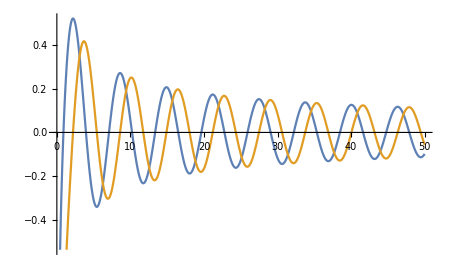

```mathematica
Plot[{BesselY[0,x],BesselY[1,x]},{x,0,50}]
```

```mathematica
Plot3D[BesselY[0,√(x^2+ y^2)],{x,-50,50},{y,-50,50},PlotPoints->200]
```

-Graphics3D-

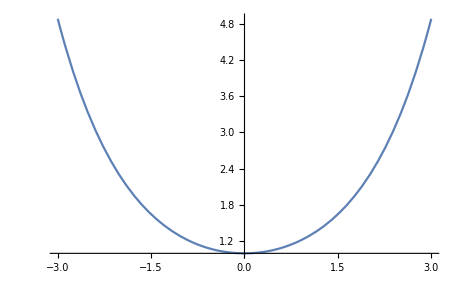

```mathematica
Plot[BesselI[0,x],{x,-3,3}]
```

```mathematica
Plot3D[BesselI[0,√(x^2+ y^2)],{x,-4,4},{y,-4,4}, PlotPoints->100,PlotRange->All]
```

-Graphics3D-

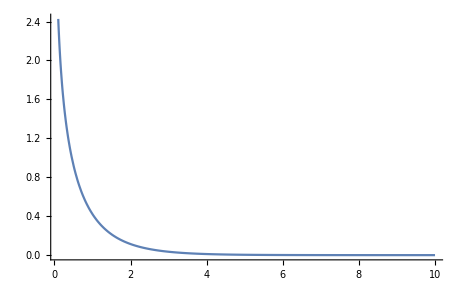

```mathematica
Plot[BesselK[0,x],{x,0.1,10},PlotRange->All]
```

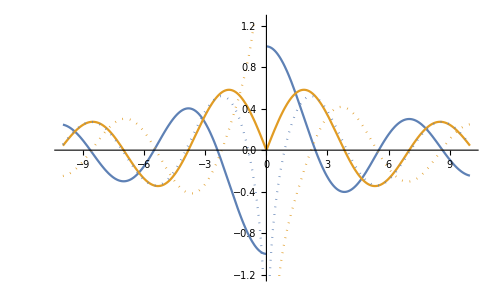

```mathematica
ReImPlot[{HankelH1[0,x],HankelH1[1,x]},{x,-10,10}]
```

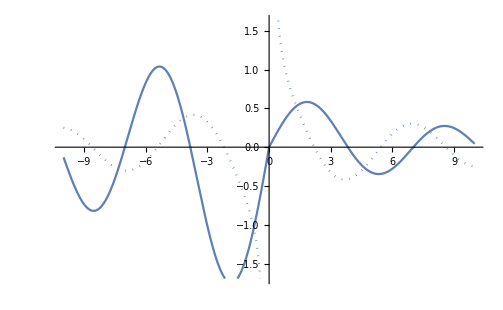

```mathematica
ReImPlot[HankelH2[1,x],{x,-10,10}]
```

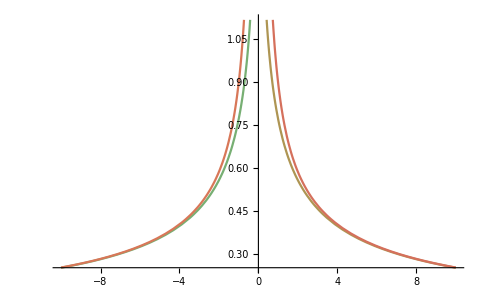

```mathematica
AbsArgPlot[{HankelH1[0,x],HankelH1[1,x]},{x,-10,10}]
```